```mathematica
FunctionExpand[DSolve[ψ''[x]+(b-1/x) ψ[x] == 0, ψ[x],x]]
```

{{ψ[x]→ⅇ^((-√-b+√b) x-√b x) x C[2] Hypergeometric1F1[1+(-2 (-1-2 √b)-4 √b)/(4 √-b),2,2 √-b x]+(ⅇ^((-√-b+√b) x-√b x) C[1] HypergeometricU[(-2 (-1-2 √b)-4 √b)/(4 √-b),0,2 √-b x])/(2 √-b)}}

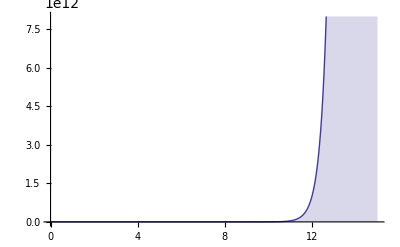

(c2 Pochhammer[1+1/(2 √-b),-1/(2 √-b)])/(2 √-b)

c1 ⅇ^(-√-b x) Hypergeometric1F1[1+1/(2 √-b),2,2 √-b x]-√-b c1 ⅇ^(-√-b x) x Hypergeometric1F1[1+1/(2 √-b),2,2 √-b x]+(1+1/(2 √-b)) √-b c1 ⅇ^(-√-b x) x Hypergeometric1F1[2+1/(2 √-b),3,2 √-b x]-(c2 ⅇ^(-√-b x) HypergeometricU[1+1/(2 √-b),1,2 √-b x])/(2 √-b)-1/2 c2 ⅇ^(-√-b x) HypergeometricU[1/(2 √-b),0,2 √-b x]

c1-c2/(2 Gamma[1-(√-b)/(2 b)])-(c2 HypergeometricU[1+1/(2 √-b),1,0])/(2 √-b)

```mathematica
f[x_, b_, c1_, c2_]=c1 Exp[-Sqrt[-b] x] x Hypergeometric1F1[1 + 1/2/Sqrt[-b], 2, 2Sqrt[-b] x] + c2 Exp[-Sqrt[-b] x] /2/Sqrt[-b]HypergeometricU[1/2/Sqrt[-b], 0, 2Sqrt[-b] x]; 
Plot[f[x, -10,0.0001, -1],{x,0,15},Filling->Bottom]
f[0, b, c1, c2]
df[x_, b_, c1_, c2_] =D[f[x,b,c1,c2], x]
FunctionExpand[df[0, b, c1, c2]]
```